```mathematica
Clear[w,wo,wzx,wzy]
Clear[nx,ny,nz,ξ]
w=1;
wo=1;
wzx [nx_,nz_]:= wo √(1-(nz-nx)/wo);
wzy[ny_,nz_]:=1-(nz-ny)/wo;
Clear[ϵ1mn,ϵ1pn,ϵ2mn,ϵ2pn]
ϵ1mn[nx_,nz_,q_]:= √(1/2*((w^2+wzx[nx,nz]^2)-√((wzx[nx,nz]^2-w^2)^2+4*w^2*wzx[nx,nz]^2*q^2)));
ϵ1pn[nx_,nz_,q_]:= √(1/2*((w^2+wzx[nx,nz]^2)+√((wzx[nx,nz]^2-w^2)^2+4*w^2*wzx[nx,nz]^2*q^2)));
ϵ2mn[nx_,ny_,nz_,q_,ξ_]:= √(1/2*((1+wzy[ny,nz])-√((wzy[ny,nz]-1)^2+4*(1-ξ)^2/(1+ξ)^2*q^2*wzx[nx,nz]^2/wo^2)));
ϵ2pn[nx_,ny_,nz_,q_,ξ_]:= √(1/2*((1+wzy[ny,nz])+√((wzy[ny,nz]-1)^2+4*(1-ξ)^2/(1+ξ)^2*q^2*wzx[nx,nz]^2/wo^2)));
(*NORMAL vibrational modes*)

Clear[ϵ1mϵ2mn,ϵ1pϵ2pn]
ϵ1mϵ2mn[nx_,ny_,nz_,q_,ξ_]:=Re[ϵ1mn[nx,nz,q]*ϵ2mn[nx,ny,nz,q,ξ]];
ϵ1pϵ2pn[nx_,ny_,nz_,q_,ξ_]:=Re[ϵ1pn[nx,nz,q]*ϵ2pn[nx,ny,nz,q,ξ]];

(*Superradiant Phase*)
Clear[μx,wa,wb,wc,wd]
μx[nx_,nz_,q_] := 1/(wzx[nx,nz]^2/wo^2*(q^2-1)+1);
wa[nx_,nz_,q_]:=1/2*((wo/μx[nx,nz,q]-nz)*(1+μx[nx,nz,q])+nx*(1-μx[nx,nz,q]));
wb[nx_,nz_,q_]:=(1-μx[nx,nz,q])/8*(wo/(1+μx[nx,nz,q])*(3+μx[nx,nz,q])/μx[nx,nz,q]+nz+nx*((3*μx[nx,nz,q]^2-2*μx[nx,nz,q]+3)/(1-μx[nx,nz,q]^2)));
wc[nx_,ny_,nz_,q_]:=-1/8*ny*(1+μx[nx,nz,q]);
wd[nx_,nz_,q_]:=-(√2)/4*q*√(w/wo)*wzx[nx,nz]*(1-μx[nx,nz,q])/(√(1+μx[nx,nz,q]));
(*Mix Frequencies*)
Clear[w1,w2,w3]
w1[nx_,nz_,q_]:=wa[nx,nz,q]^2*(1+4*wb[nx,nz,q]/wa[nx,nz,q]);
w2[nx_,nz_,q_]:=√(w*wa[nx,nz,q])*(4*wd[nx,nz,q]+√2*q*√(w/wo)*wzx[nx,nz]*√(1+μx[nx,nz,q]));
w3[nx_,ny_,nz_,q_]:=1-4*wc[nx,ny,nz,q]/wa[nx,nz,q];
w4[nx_,nz_,q_,ξ_]:=(√2)/(√(wo*wa[nx,nz,q]))*wzx[nx,nz]*q*√(1+μx[nx,nz,q])*(1-ξ)/(1+ξ);
(*SUPERRADIANT vibrational modes*)
Clear[ϵ1ms,ϵ1ps,ϵ2ms,ϵ2ps,ϵ1mϵ2ms,ϵ1pϵ2ps]
ϵ1ms[nx_,ny_,nz_,q_]:=√(1/2*((w^2+w1[nx,nz,q]^2)-√((w^2-w1[nx,nz,q]^2)^2+w2[nx,nz,q]^2)));
ϵ1ps[nx_,ny_,nz_,q_]:=√(1/2*((w^2+w1[nx,nz,q]^2)+√((w^2-w1[nx,nz,q]^2)^2+w2[nx,nz,q]^2)));


ϵ2ms[nx_,ny_,nz_,q_,ξ_]:=√(1/2*((1+w3[nx,ny,nz,q])-√((w3[nx,ny,nz,q]-1)^2+w4[nx,nz,q,ξ]^2)));
ϵ2ps[nx_,ny_,nz_,q_,ξ_]:=√(1/2*((1+w3[nx,ny,nz,q])+√((w3[nx,ny,nz,q]-1)^2+w4[nx,nz,q,ξ]^2)));


ϵ1mϵ2ms[nx_,ny_,nz_,q_,ξ_]:=Re[ϵ1ms[nx,ny,nz,q]*ϵ2ms[nx,ny,nz,q,ξ]];
ϵ1pϵ2ps[nx_,ny_,nz_,q_,ξ_]:=Re[ϵ1ps[nx,ny,nz,q]*ϵ2ps[nx,ny,nz,q,ξ]];

Clear[solutionsInferior,solutionsSuperior]
solutionsInferior[nx_,ny_,nz_,ξ_]:=FindRoot[ϵ1mϵ2mn[nx,ny,nz,q,ξ]==ϵ1mϵ2ms[nx,ny,nz,q,ξ],{q,1.1}]
solutionsSuperior[nx_,ny_,nz_,ξ_]:=FindRoot[ϵ1pϵ2pn[nx,ny,nz,q,ξ]==ϵ1pϵ2ps[nx,ny,nz,q,ξ],{q,1.1}]
Clear[q1,q2]
q1[nx_,ny_,nz_,ξ_]:=q/.solutionsInferior[nx,ny,nz,ξ]
q2[nx_,ny_,nz_,ξ_]:=q/.solutionsSuperior[nx,ny,nz,ξ]
```

```mathematica
(*Variables del plot*)
Clear[cB,cT,align,scale]
cB=Black;
cT=Transparent;
align[Center]={0,0};  
scale=600;
Clear[pt1a,pt2a,pt3,pt4a]
pt1a[nx_,ny_,nz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=Plot[ϵ1mϵ2mn[nx,ny,nz,q,ξ],{q,0,q1[nx,ny,nz,ξ]},
Frame->True,
PlotRange->{{0,6},{-0.5,4}},
FrameTicks->{{{0,1,2,3,4,5,6},None},{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},None}},
FrameTicksStyle->Directive[FontSize->20,Black],
FrameLabel->{Style["γ/γ_ξx^c",FontSize->35,ejex],Style["ϵ_±",FontSize->35,ejey]},
PlotStyle->Black,
ImageSize->scale,
Epilog->{Text[Style["ϵ_-^N",FontSize->22,Black],{x1,y1},align[Center]],
Text[Style["ϵ_-^S",FontSize->22,Black],{x2,y2},align[Center]],
Text[Style["ϵ_+^N",FontSize->22,Black],{x3,y3},align[Center]],
Text[Style["ϵ_+^S",FontSize->22,Black],{x4,y4},align[Center]],
Inset[Framed[Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[nx]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(y\)]\)="<>ToString[ny]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(z\)]\)="<>ToString[nz],23.5],Background->LightYellow],{6,4.01},{1,1}],Inset[Framed[Style["ξ="<>ToString[ξ],23.5],Background->LightYellow],{6,3.47},{1,1}],{Line[{{1,-1},{1,4}}]},{Directive[ColorData["HTML","Gray"],Thickness[0.001]],Line[{{-5,1},{6,1}}]},{Dashed,Directive[ColorData["HTML","Purple"],Thickness[0.0035]],Line[{{g1,-1},{g1,4}}]},{Dashed,Directive[ColorData["HTML","DarkOrange"],Thickness[0.0035]],Line[{{g2,-1},{g2,4}}]},{Dashed,Directive[ColorData["HTML","RoyalBlue"],Thickness[0.0035]],Line[{{g3,-1},{g3,4}}]}}]
pt2a[nx_,ny_,nz_,ξ_]:=Plot[ϵ1mϵ2ms[nx,ny,nz,q,ξ],{q,q1[nx,ny,nz,ξ],6},Frame->True,
FrameTicks->{{{0,1,2,3,4,5,6},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,6}},
PlotStyle->Black,
ImageSize->scale
];
pt3[nx_,ny_,nz_,ξ_]:=Plot[ϵ1pϵ2pn[nx,ny,nz,q,ξ],{q,0,q2[nx,ny,nz,ξ]},Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->Black,
ImageSize->scale
];
pt4a[nx_,ny_,nz_,ξ_]:=Plot[ϵ1pϵ2ps[nx,ny,nz,q,ξ],{q,q2[nx,ny,nz,ξ],6},Frame->True,
FrameTicks->{{{0,1,2,3,4,6},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,6}},
PlotStyle->Black,
ImageSize->scale
];
Clear[pa]
pa[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=Show[pt1a[ηx,ηy,ηz,ξ,ejex,ejey,x1,y1,x2,y2,x3,y3,x4,y4,g1,g2,g3],pt2a[ηx,ηy,ηz,ξ],pt3[ηx,ηy,ηz,ξ],pt4a[ηx,ηy,ηz,ξ],Background->White]

Clear[pt1,pt2,pt4]
pt1[nx_,ny_,nz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=Plot[ϵ1mϵ2mn[nx,ny,nz,q,ξ],{q,0,q1[nx,ny,nz,ξ]},Frame->True,
PlotRange->{{0,3.1},{-0.5,4}},
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
FrameTicksStyle->Directive[FontSize->20,Black],
FrameLabel->{Style["γ/γ_ξx^c",FontSize->35,ejex],Style["ϵ_±",FontSize->35,ejey]},
PlotStyle->Black,
ImageSize->scale,
Epilog->{Text[Style["ϵ_-^N",FontSize->22,Black],{x1,y1},align[Center]],
Text[Style["ϵ_-^S",FontSize->22,Black],{x2,y2},align[Center]],
Text[Style["ϵ_+^N",FontSize->22,Black],{x3,y3},align[Center]],
Text[Style["ϵ_+^S",FontSize->22,Black],{x4,y4},align[Center]],
Inset[Framed[Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[nx]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(y\)]\)="<>ToString[ny]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(z\)]\)="<>ToString[nz],23.5],Background->LightYellow],{3.1,4.01},{1,1}],Inset[Framed[Style["ξ="<>ToString[ξ],23.5],Background->LightYellow],{3.1,3.47},{1,1}],{Line[{{1,-1},{1,4}}]},{Directive[ColorData["HTML","Gray"],Thickness[0.001]],Line[{{-5,1},{5,1}}]},{Dashed,Directive[ColorData["HTML","Purple"],Thickness[0.0035]],Line[{{g1,-1},{g1,4}}]},{Dashed,Directive[ColorData["HTML","DarkOrange"],Thickness[0.0035]],Line[{{g2,-1},{g2,4}}]},{Dashed,Directive[ColorData["HTML","RoyalBlue"],Thickness[0.0035]],Line[{{g3,-1},{g3,3}}]}}]
pt2[nx_,ny_,nz_,ξ_]:=Plot[ϵ1mϵ2ms[nx,ny,nz,q,ξ],{q,q1[nx,ny,nz,ξ],4},Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->Black,
ImageSize->scale
];

pt4[nx_,ny_,nz_,ξ_]:=Plot[ϵ1pϵ2ps[nx,ny,nz,q,ξ],{q,q2[nx,ny,nz,ξ],4},Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->Black,
ImageSize->scale
];
Clear[p]
p[nx_,ny_,nz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=Show[pt1[nx,ny,nz,ξ,ejex,ejey,x1,y1,x2,y2,x3,y3,x4,y4,g1,g2,g3],pt2[nx,ny,nz,ξ],pt3[nx,ny,nz,ξ],pt4[nx,ny,nz,ξ],Background->White]
```

```mathematica
(** Variables  **)
Subscript[ω, o]=1;
(** Ecuación Superficie de energía general  **)
Clear[Ecl0]
Ecl0[x_,y_,q_,ξ_,nx_,ny_,nz_]:=If[x^2+y^2<3.2Pi,1/(2*(x^2+y^2))*(Sin[Sqrt[x^2+y^2]])^2*(x^2*(nx/Subscript[ω, o]-q^2*(1+ξ)^2)+y^2*(ny/Subscript[ω, o]-q^2*(1-ξ)^2))-Cos[Sqrt[x^2+y^2]]*(1-nz/(2 Subscript[ω, o])Cos[Sqrt[x^2+y^2]]),Null];
Clear[LB,EC0]
(*********************************************************2********************************************************************************)
LB1=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC1=ContourPlot[{Ecl0[x,y,0.3,0,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,White],Style["v",FontSize->25,Black]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 0.3γ_(0+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{Black,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ = 0.3γ_(0  x)^c",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","Purple"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf1=Show[EC1,LB1,Graphics[{Green,AbsolutePointSize[13.0],Point[{0,0}]}]];
(*********************************************************5********************************************************************************)
LB2=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC2=ContourPlot[{Ecl0[x,y,1.1,0,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Transparent],Style["v",FontSize->25,Transparent]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = γ_(0+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ = 1.1γ_(0  x)^c",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","DarkOrange"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf2=Show[EC2,LB2,Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{0.59803013738355,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-0.59803013738355,0}]}]];

(*********************************************************8********************************************************************************)
LB3=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC3=ContourPlot[{Ecl0[x,y,3,0,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,White],Style["v",FontSize->25,Transparent]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 3γ_(0+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style[StringJoin[{"γ = 3γ_(0  x)^c"}],30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","RoyalBlue"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf3=Show[EC3,LB3,Graphics[{Red,AbsolutePointSize[13.0],Point[{0,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{1.459455,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-1.459455,0}]}],Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,1.447023753236062}]}],Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,-1.447023753236062}]}]];

(*********************************************************2********************************************************************************)
LB4=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC4=ContourPlot[{Ecl0[x,y,0.3,0.5,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Transparent],Style["v",FontSize->25,Black]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 0.3γ_(0.5+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{Black,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ = 0.3γ_(0.5  x)^c",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","Purple"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf4=Show[EC4,LB4,Graphics[{Green,AbsolutePointSize[13.0],Point[{0,0}]}]];
(*********************************************************5********************************************************************************)
LB5=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC5=ContourPlot[{Ecl0[x,y,1.1,0.5,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Transparent],Style["v",FontSize->25,Transparent]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = γ_(0.5+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ = 1.1γ_(0.5  x)^c",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","DarkOrange"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf5=Show[EC5,LB5,Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{1.194681712744674,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-1.194681712744674,0}]}]];
(*********************************************************8********************************************************************************)
LB6=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC6=ContourPlot[{Ecl0[x,y,3,0.5,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Black],Style["v",FontSize->25,White]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 3γ_(0.5+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ = 3γ_(0.5  x)^c",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","RoyalBlue"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf6=Show[EC6,LB6,Graphics[{Green,AbsolutePointSize[13.0],Point[{1.521393517472283,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-1.521393517472283,0}]}],Graphics[{Red,AbsolutePointSize[13.0],Point[{0,0}]}]];
(*********************************************************2********************************************************************************)
LB7=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC7=ContourPlot[{Ecl0[x,y,0.3,1,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Black],Style["v",FontSize->25,Black]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 0.3γ_(1+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{Black,White},{Black,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ = 0.3γ_(1  x)^c",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","Purple"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf7=Show[EC7,LB7,Graphics[{Green,AbsolutePointSize[13.0],Point[{0,0}]}]];

(*********************************************************5********************************************************************************)
LB8=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC8=ContourPlot[{Ecl0[x,y,1.1,1,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Black],Style["v",FontSize->25,Transparent]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = γ_(1+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{Black,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ = 1.1γ_(1  x)^c",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","DarkOrange"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf8=Show[EC8,LB8,Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{1.362685795276514,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-1.362685795276514,0}]}]];
(*********************************************************8********************************************************************************)
LB9=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC9=ContourPlot[{Ecl0[x,y,3,1,0,0.9,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Black],Style["v",FontSize->25,Transparent]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 3γ_(1+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{Black,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0, (η̃)_y=0.9, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ = 3γ_(1  x)^c",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","RoyalBlue"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf9=Show[EC9,LB9,Graphics[{Green,AbsolutePointSize[13.0],Point[{ArcCos[1/36],0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-ArcCos[1/36],0}]}],Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,0}]}]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

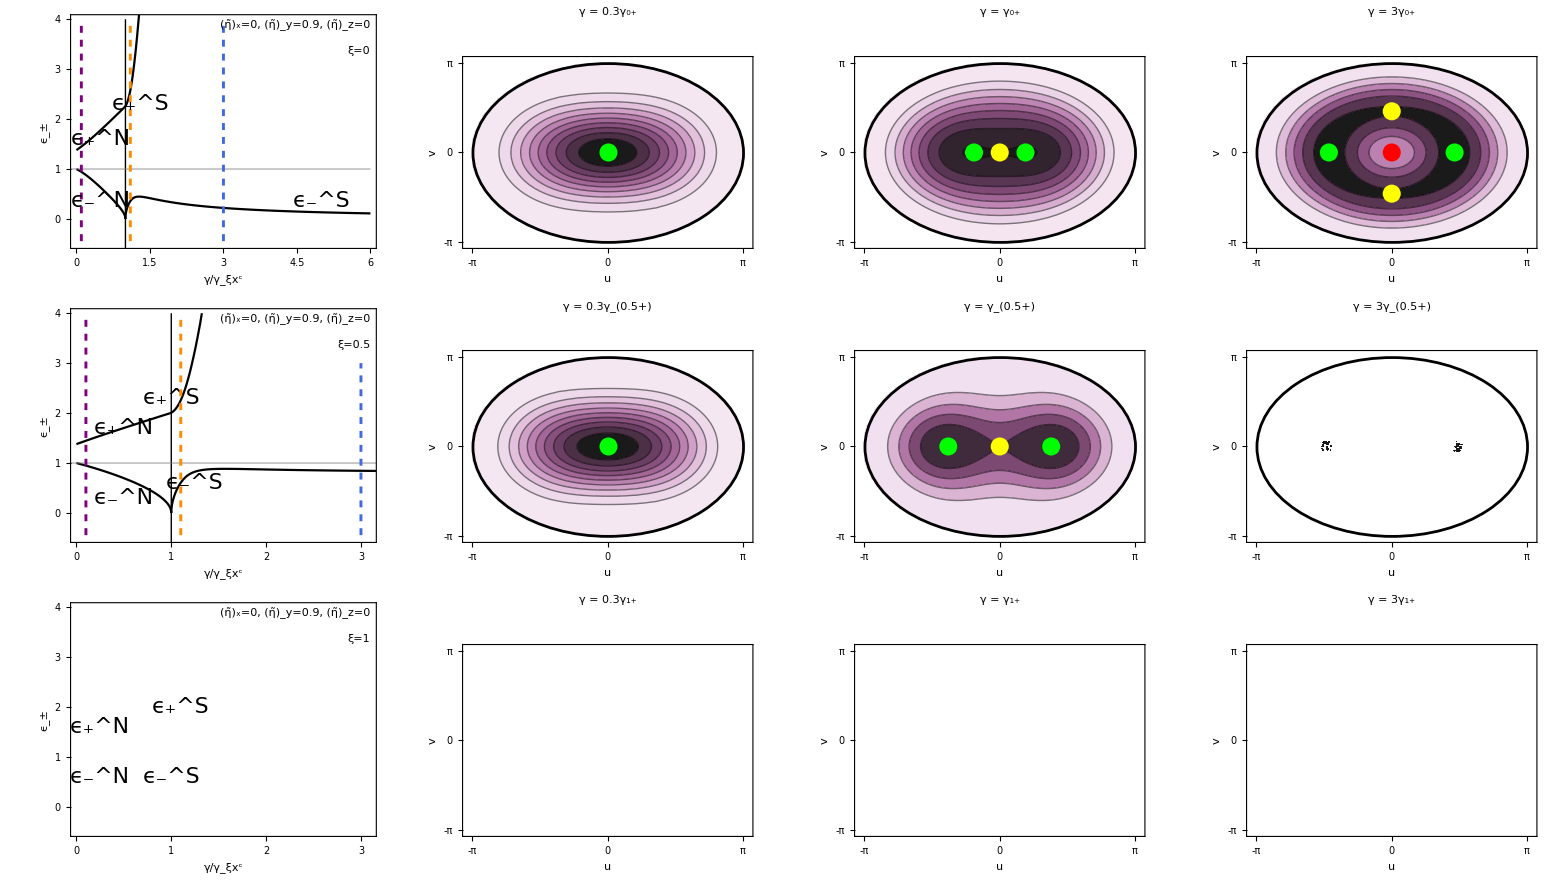

```mathematica
SetDirectory["/Users/rich/Documentos/07 Trimestre/Entropy Campo Medio/Gamma_Scaled/0_9"];
exp=Grid[{{pa[0,0.9,0,0,cB,cB,0.5,0.35,5,0.35,0.5,1.6,1.3,2.3,0.1,1.1,3],Surf1,Surf2,Surf3},
{p[0,0.9,0,0.5,cB,cB,0.5,0.3,1.25,0.6,0.5,1.7,1,2.3,0.1,1.1,3],Surf4,Surf5,Surf6},{p[0,0.9,0,1,cB,cB,0.25,0.6,1,0.6,0.25,1.6,1.1,2,0.1,1.1,3],Surf7,Surf8,Surf9}}]
Export["y-interaction.png",exp,ImageSize-> 2000,"CompressionLevel"->0,Background->White];
```